```mathematica
Clear[ϵ]
```

```mathematica
(1/(50*365))/((1/(50*365))+1/7)
```

7/18257

```mathematica
S=(1/R)-(2p/((R-1)+√((R-1)^2+4*R*p)))
```

1/R-(2 p)/(-1+R+√((-1+R)^2+4 p R))

```mathematica
V=(ϵ*(R-1)+ϵ*√((R-1)^2+4*R*p))/(2*R)
```

(1/2 (-1+R)+1/2 √((-1+R)^2+4 p R))/(2 R)

```mathematica
ϵ=5/10
```

1/2

```mathematica
Solve[(1-R S+R V+ϵ)^2-4 (R V+ϵ-R S ϵ)==0,p]
```

{{p→(-16 R+75 R^2-18 R^3-2 √2 √(-49 R^2+105 R^3+117 R^4+27 R^5))/(81 R^2)},{p→(-16 R+75 R^2-18 R^3+2 √2 √(-49 R^2+105 R^3+117 R^4+27 R^5))/(81 R^2)}}

```mathematica
Clear[p]
```

```mathematica
g[R_]:=(-16 R+75 R^2-18 R^3+2 √2 √(-49 R^2+105 R^3+117 R^4+27 R^5))/(81 R^2)
```

```mathematica
h[R_]:=g[R+1]
```

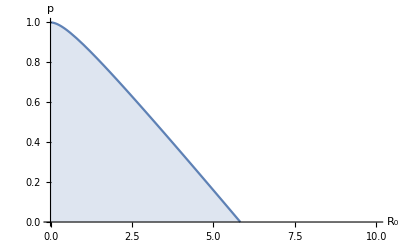

```mathematica
Plot[h[R],{R,0,10},Filling->Bottom,AxesLabel->{Subscript[R, 0],p},PlotRange->{{0,10},{0,1}}]
```

LogLinearPlot::invpr: Value of option PlotRange should be positive in the scaled dimensions.

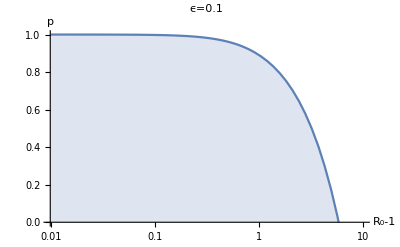

```mathematica
LogLinearPlot[h[R],{R,0,10},Filling->Bottom,AxesLabel->{"R_0-1",p},PlotRange->{{0,10},{0,1}},PlotLabel->"ϵ=0.5"]
```

```mathematica
Export["C:\\Users\\Roger Zhang\\Documents\\GitHub\\RogerZhang\\July_6th\\Figures\\epsilon_0.5.pdf",%76,"PDF"]
```

C:\Users\Roger Zhang\Documents\GitHub\RogerZhang\July_6th\Figures\epsilon_0.5.pdf